```mathematica
Magnetic  structure  of  EuPtIn4 , q (1/2 1/2   0.43);
```

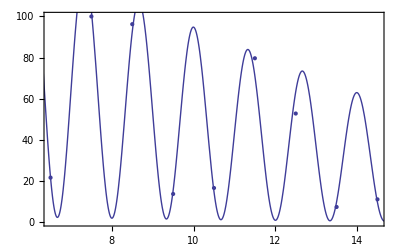

{-0.018567,-2.56401,3.6575,-1.72346,1.8552,8.5777,-10.6524,-2.50871,1.50695}

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
ma | 0.0206914 | 0.00767111 | {0.000972219,0.0404106}
mb | 0.0255478 | 0.0795822 | {-0.179025,0.23012}
mc | -0.291163 | 0.207962 | {-0.825747,0.243421}
R | 14523.1 | 2.14244×10^-6 | {14523.1,14523.1}

```mathematica
ClearAll[P1,P2,P3,Z1,Z2,Z3,θ,F1,F2,A,k,θ,F1,F2,k,Za,Zb,Zc,P1,P2,P3,bet,alp,chi,za1,zb1,za2,zb2,h,k,l,A,z1k,z2k,z3k,Fact1,Fact2,Int,ma,mb,mc,magmoment,projectedmagmoment,z11,z12,z13,z21,z31,z32,z22,f11,f12,f13,f21,f22,f23,f31,f32,f33,intensitydata,R];
θ[k_]:=0.5*(-98.22284+105.69129*Exp[k/25.19289]);
alp[k_]:=24.79091+3.6745*Exp[k/7.28251];
bet[k_]:=(2*θ[k]-alp[k])*π/180;
chi[k_]:=(85.967173-24.03565*Exp[-k*0.20485])*π/180;
Lorentz[k_]:=1/Sin[2*θ[k]*Pi/180];
Absorp[k_]:=1/(1+(Sin[alp[k]*Pi/180]/Sin[bet[k]*Pi/180]));

deltaplus=ⅇ^(-2*π*ⅈ*0.215);
deltaminus=ⅇ^(-2*π*ⅈ*0.715);
qhkl[h_,k_,l_]:=2π *{h,k,l};
r1={0,0.3748,1/4}; x=0;y=0.3748;z=1/4;
r2={0,-0.3748,3/4};
h=1/2;
l=0.4258;
A=1;

(*Fact1[za1_,zb1_,k_]:=(-za1 Cos[θ[k]*π/180]+zb1 Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(h x+k y+l z))
Fact2[za2_,zb2_,k_]:=(-za2 Cos[θ[k]*π/180]+zb2 Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(-h x-k y+l( z+l/2)-0.215))
Int[za1_,zb1_,za2_,zb2_,k_]:=ComplexExpand[((-za1 Cos[θ[k]*π/180]+zb1 Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(h x+k y+l z))+(-za2 Cos[θ[k]*π/180]+zb2 Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(-h x - k y + l( z + l/2)))*ⅇ^(-2π ⅈ 0.215))]^2*)

(*f11[k_]:=0.15971+0.00767 ⅇ^(0.16926 k);   f12[k_]:=-0.00766-0.03777 ⅇ^(-0.29455 k);  f13[k_]:=-0.0263+0.00357k-0.000245 k^2+0.00000492 k^3;  
f21[k_]:=0.00538+0.02592 ⅇ^(-0.29405 k);  f22[k_]:=-0.00153-0.04312 ⅇ^(-0.3268 k);   f23[k_]:=0.05261+0.25999 ⅇ^(-0.29512 k);
f31[k_]:=-0.02178-0.88385 ⅇ^(-0.29885 k);  f32[k_]:=-0.04455-0.29436 ⅇ^(-0.175 k);   f33[k_]:=-0.00707-0.28703 ⅇ^(-0.29874 k);*)

f11[k_]:=1.37295-0.32119 ⅇ^(-k/3.29386);   f12[k_]:=-0.03117-0.2194 ⅇ^(-k/5.33731);  f13[k_]:=-0.05853-0.22177 ⅇ^(-k/3.23388);  
f21[k_]:=0.08663-0.01017 ⅇ^(-k/3.65822);  f22[k_]:=-0.02014-0.15611 ⅇ^(-k/4.91096);   f23[k_]:=0.84694-0.0798 ⅇ^(-k/3.14435);
f31[k_]:=-0.12269-0.88628 ⅇ^(-k/5.20381);  f32[k_]:=-0.36794+0.11169 ⅇ^(-k/3.27971);   f33[k_]:=-0.03987-0.288 ⅇ^(-k/5.20376);


Trans[k_]:={{f11[k],f12[k],f13[k]},{f21[k],f22[k],f23[k]},{f31[k],f32[k],f33[k]}}  (* Transformation from the ... to ... *)
Trans[k]//MatrixForm;
(*AAM=Trans[k].{0,0,1};
AAM//MatrixForm
AAM2=Trans[k].{0,0,-1};
AAM2//MatrixForm*)

AA=Trans[k].{0.71218933,-0.41377737,-0.08995832};
AAi={5.061926,-5.11525977,-0.89189431}.Trans[k] (*wrong*);
BB=Trans[k].{0.04503414,-0.25730434 ,1.16834286};
CC=Trans[k].{-0.11539633,-2.65411647,-0.09924092};
(*AA=Trans[k].{5.061926,-5.11525977,-0.89189431};
AAi={5.061926,-5.11525977,-0.89189431}.Trans[k] (*wrong*);
BB=Trans[k].{0.4097742,-4.16239153 ,10.68885441};
CC=Trans[k].{-0.50000002,-6.49999985,-0.4300001};*)
magmoment[ma_,mb_,mc_]:={ma,mb,mc};
projectedmagmoment[k_,ma_,mb_,mc_]:=Trans[k].magmoment[ma,mb,mc];
projectedmagmomentalongu1[k_,ma_,mb_,mc_]:=projectedmagmoment[k,ma,mb,mc][[1]]
projectedmagmomentalongu2[k_,ma_,mb_,mc_]:=projectedmagmoment[k,ma,mb,mc][[2]]
projectedmagmomentalongu3[k_,ma_,mb_,mc_]:=projectedmagmoment[k,ma,mb,mc][[3]]
z11[k_,ma_,mb_,mc_]:=projectedmagmomentalongu1[k,ma,mb,mc]
z21[k_,ma_,mb_,mc_]:=projectedmagmomentalongu2[k,ma,mb,mc]
z31[k_,ma_,mb_,mc_]:=projectedmagmomentalongu3[k,ma,mb,mc]
z12[k_,ma_,mb_,mc_]=-z11[k,ma,mb,mc];
z22[k_,ma_,mb_,mc_]=-z21[k,ma,mb,mc];
z32[k_,ma_,mb_,mc_]=z31[k,ma,mb,mc];

(*Fact1=(-za1 Cos[θ[k]*π/180]+zb1 Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(h x + k y + l z));
Fact2=(-za1 Cos[θ[k]*π/180]+zb1 Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(-h x - k y + l( z + 1/2)))*ⅇ^(-2π ⅈ 0.215A);
Int=ComplexExpand[Abs[(Fact1+Fact2)]]^2;*)
CS1[k_,ma_,mb_,mc_]:={-z11[k,ma,mb,mc] Cos[θ[k]*π/180],0,z31[k,ma,mb,mc]Sin[θ[k]*π/180]}ⅇ^(2π ⅈ(h x + k y + l z))
CS2[k_,ma_,mb_,mc_]:={-z12[k,ma,mb,mc] Cos[θ[k]*π/180],0,z32[k,ma,mb,mc]Sin[θ[k]*π/180]}ⅇ^(2π ⅈ(-h x - k y + l( z + 1/2)))*ⅇ^(-2π ⅈ 0.215)
CS1pipi[k_,ma_,mb_,mc_]:={0,z21[k,ma,mb,mc] Sin[2θ[k]*π/180],0}ⅇ^(2π ⅈ(h x + k y + l z))
CS2pipi[k_,ma_,mb_,mc_]:={0,z22[k,ma,mb,mc] Sin[2θ[k]*π/180],0}ⅇ^(2π ⅈ(-h x - k y + l( z + 1/2)))*ⅇ^(-2π ⅈ 0.215)
CS1pisi[k_,ma_,mb_,mc_]:={z11[k,ma,mb,mc] Cos[θ[k]*π/180],0,z31[k,ma,mb,mc]Sin[θ[k]*π/180]}ⅇ^(2π ⅈ(h x + k y + l z))
CS2pisi[k_,ma_,mb_,mc_]:={z12[k,ma,mb,mc] Cos[θ[k]*π/180],0,z32[k,ma,mb,mc]Sin[θ[k]*π/180]}ⅇ^(2π ⅈ(-h x - k y + l( z + 1/2)))*ⅇ^(-2π ⅈ 0.215)
(*z11=-z12; z31=z32;*)
(*Fact1=(-za1 Cos[θ[k]*π/180]+zb1 Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(h x + k y + l z));
Fact2=(-za1 Cos[θ[k]*π/180]+zb1 Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(-h x - k y + l( z + 1/2)))*ⅇ^(-2π ⅈ 0.215A);
Int=ComplexExpand[Abs[(Fact1+Fact2)]]^2;*)


Int[k_,z11_,z31_,z12_,z32_]:=ComplexExpand[Abs[(Fact1[k,z11,z31]+Fact2[k,z12,z32])]]^2;

Intb[k_,ma_,mb_,mc_,R_]:=R Abs[(CS1[k,ma,mb,mc] +CS2[k,ma,mb,mc] ).(Conjugate[ CS1[k,ma,mb,mc] + CS2[k,ma,mb,mc] ])] ;

Intpipi[k_,ma_,mb_,mc_,R_]:=R Abs[(CS1pipi[k,ma,mb,mc] +CS2pipi[k,ma,mb,mc] ).(Conjugate[ CS1pipi[k,ma,mb,mc] + CS2pipi[k,ma,mb,mc] ])] 
Intpisi[k_,ma_,mb_,mc_,R_]:=R Abs[(CS1pisi[k,ma,mb,mc] +CS2pisi[k,ma,mb,mc] ).(Conjugate[ CS1pisi[k,ma,mb,mc] + CS2pisi[k,ma,mb,mc] ])] 


model=Intb[k,ma,mb,mc,R];
intensitydata={{6.5,21.55},{7.5,100},{8.5,96.24},{9.5,13.6},{10.5, 16.5},{11.5, 79.65},{12.5, 52.75},{13.5, 7.26},{14.5, 10.97}};
intensitydatab={{6.5,0.2155},{7.5,1},{8.5,0.9624},{9.5,0.136},{10.5,0.165},{11.5, 0.7965},{12.5, 0.5275},{13.5, 0.0726},{14.5, 0.1097}};
nlm=NonlinearModelFit[intensitydata,{model,{-1.01<ma<1.01,-1.01<mb<1.01,-1.01<mc<1.01,1<R<10000000}},{ma,mb,mc,R},k,Method->"NMinimize"] ;
Show[ListPlot[intensitydata],Plot[nlm[k],{k,5.5,17}],Frame->True]

nlm["FitResiduals"]
ListPlot[%,Filling->Axis];
nlm["ParameterConfidenceIntervalTable"]

(*Show[Plot[nlm,{k,5.5,14.5}],ListPlot[intensitydata,PlotRange->All]]*)
```

```mathematica
(*ratio=Intpisi[11.5,1,-0.6,0.4,1]/Intpipi[11.5,1,-0.6,0.4,1]*)
```

```mathematica
Intb[k_,ma_,mb_,mc_,R_]:=R Abs[(CS1[k,ma,mb,mc] +CS2[k,ma,mb,mc] ).(Conjugate[ CS1[k,ma,mb,mc] + CS2[k,ma,mb,mc] ])] ;
R=1;
Manipulate[Dynamic@Show[Plot[{100*Intb[k,ma,mb,mc,R]/Intb[7.5,ma,mb,mc,R]},{k,6,15},Frame->True,AxesLabel->{"k value "},PlotLabel->Style["Int",FontSize->22],Background->LightGray,PlotStyle->{Darker[Red],Dashed,Thick}],   ListPlot[{{6.5,21.55},{7.5,100},{8.5,96.24},{9.5,13.6},{10.5, 16.5},{11.5, 79.65},{12.5, 52.75},{13.5, 7.26},{14.5, 10.97}},PlotStyle->Darker[Green],PlotMarkers->{Automatic,Medium}],PlotRange->{Automatic,{0,130}},AxesOrigin->{5.5,50}],{ma,1,-1},{mb,1,-1},{mc,1,-1}]
```

FittedModel[964.378 Abs[(0.+0. ⅈ)+Conjugate[«1»] («1»)+Conjugate[«1»] («1»)]]

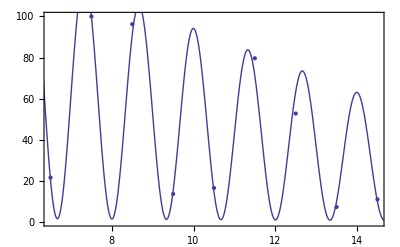

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
ma | -0.0888328 | 434644. | {-1.06354×10^6,1.06354×10^6}
mb | -0.0442335 | 216427. | {-529578.,529578.}
mc | 0.900448 | 4.40575×10^6 | {-1.07805×10^7,1.07805×10^7}

(0 | (-0.865973+0.500091 ⅈ) (0.826042 za1+0.563608 zb1)+(0.273859-0.96177 ⅈ) (0.826042 za2+0.563608 zb2)
(-0.865973+0.500091 ⅈ) (-0.826042 za1+0.563608 zb1)+(0.273859-0.96177 ⅈ) (-0.826042 za2+0.563608 zb2) | (0.806332-0.465649 ⅈ) zc1-(0.254997-0.895531 ⅈ) zc2).{{0.213431,-0.00893659,-0.0101635},{0.00626112,-0.0025358,0.06134},{-0.0502119,-0.0838924,-0.0163149}}

```mathematica
intensitydataint={{6.5,21.55},{7.5,100},{8.5,96.24},{9.5,13.6},{10.5, 16.5},{11.5, 79.65},{12.5, 52.75},{13.5, 7.26},{14.5, 10.97}};
model1=100*Intb[k,ma,mb,mc,1]/Intb[7.5,ma,mb,mc,1];
nlm=NonlinearModelFit[intensitydataint,{model1,{-1.01<ma<1.01,-1.01<mb<1.01,-1.01<mc<1.01}},{ma,mb,mc},k,Method->"NMinimize"] 
Show[ListPlot[intensitydata],Plot[nlm[k],{k,6,15}],Frame->True]
nlm["FitResiduals"];

ListPlot[%,Filling->Axis];
nlm["ParameterConfidenceIntervalTable"]
```

```mathematica
ClearAll[P1,P2,P3,Z1,Z2,Z3,θ,F1,F2,A,h,k,l,θ,F1,F2,Za,Zb,Zc,P1,P2,P3,bet,alp,chi,za1,zb1,za2,zb2,zc1,zc2,ang1,ang2,ang3,ang4,z1,z2,z3,za1,za2,zb1,zb2,AA,projectedmagmoment,projectedmagmomentalongu1,projectedmagmomentalongu2,projectedmagmomentalongu3,magmoment];
H=0T;
θ[k_]:=0.5*(-98.22284+105.69129*Exp[k/25.19289]);
alp[k_]:=24.79091+3.6745*Exp[k/7.28251];
bet[k_]:=(2*θ[k]-alp[k])*π/180;
chi[k_]:=(85.967173-24.03565*Exp[-k*0.20485])*π/180;
Lorentz[k_]:=1/Sin[2*θ[k]*Pi/180];
Absorp[k_]:=1/(1+(Sin[alp[k]*Pi/180]/Sin[bet[k]*Pi/180]));

p1datamag=ListPlot[{{0,-0.9599},{-0.2618,-0.89558},{-0.5236,-0.68676},{-0.7854,-0.35415},{-1.0472,-0.12816},{-1.309,0.03203},{-1.5708,0.03137},{-1.8326,-0.11378},{-2.0944,-0.3264},{-2.35619,-0.51177},{-2.61799,-0.69791},{-2.87979,-0.88236},{-3.14159,-0.97357}},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}];

p2datamag=ListPlot[{{0,-0.0785},{-0.2618,0.3475},{-0.5236,0.7048},{-0.7854,0.82884},{-1.0472,0.65572},{-1.309,0.25953},{-1.5708,-0.07237},{-1.8326,-0.34954},{-2.0944,-0.51645},{-2.35619,-0.6021},{-2.61799,-0.57008},{-2.87979,-0.43126},{-3.14159,-0.11913}},PlotStyle->Red,PlotMarkers->{Automatic,Medium}];


r1={0,0.3748,1/4}; x=0;y=0.3748;z=1/4;
r2={0,-0.3748,3/4};
h=0.5;
k=8.5;
l=0.43;

(*Fact1=(-za1 Cos[bet[k]]+zb1 Sin[bet[k]])*ⅇ^(2π ⅈ(h x+k y+l z));
Fact2=(-za2 Cos[bet[k]]+zb2 Sin[bet[k]])*ⅇ^(2π ⅈ(-h x-k y+l z+l/2-0.215));
Int=Lorentz[k]*Absorp[k]*ComplexExpand[Abs[(Fact1+Fact2)]]^2;*)

(*PolAnalyzer2[η_]=1*{P1inci[η/2],P2inci[η/2]}; MatrixForm[PolAnalyzer[η]];*)
PolAnalyzer[η_]=1*{Cos[(η)],Sin[(η)]}; MatrixForm[PolAnalyzer[η]];

P1inci[η_]:=(A01+A11*Sin[Pi*(η-xc1)/(w1)]);
A01=0.0467; A11=0.9493;w1=89.898*Pi/180;xc1=-43.81*Pi/180;

P2inci[η_]:=(A02+A12*Sin[Pi*(η-xc2)/(w2)]);
A02=-0.004; A12=0.946;w2=89.8991*Pi/180;xc2=0.6952*Pi/180;


(*za1=z1; za2=z1; 
zb1=z3; zb2=z3; 
zc1=z2; zc2=-z2; *)
A=1;
k=11.5;
B1[k_,ma_,mb_,mc_]:=0;
B2[k_,ma_,mb_,mc_]:=(z11[k,ma,mb,mc]Cos[θ[k]*π/180]+z31[k,ma,mb,mc] Sin[θ[k]*Pi/180])*ⅇ^(2π ⅈ(h x+k y+l z))-(z12[k,ma,mb,mc] Cos[θ[k]*π/180]+z32[k,ma,mb,mc] Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(-h x-k y+l (z+1/2)-0.215A));
B3[k_,ma_,mb_,mc_]:=(-z11[k,ma,mb,mc]Cos[θ[k]*π/180]+z31[k,ma,mb,mc]Sin[θ[k]*Pi/180])*ⅇ^(2π ⅈ(h x+k y+l z))-(-z12[k,ma,mb,mc] Cos[θ[k]*π/180]+z32[k,ma,mb,mc] Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(-h x-k y+l( z+1/2)-0.215 A)); (*SigmaPi component only*)
B4[k_,ma_,mb_,mc_]:=-z21[k,ma,mb,mc] Sin[2 θ[k]*π/180]*ⅇ^(2π ⅈ(h x+k y+l z))-z22[k,ma,mb,mc] Sin[2 θ[k]*π/180]*ⅇ^(2π ⅈ(-h x-k y+l (z+1/2)-0.215 A));
B[k_,ma_,mb_,mc_]=  {{B1[k,ma,mb,mc],B2[k,ma,mb,mc]},{B3[k,ma,mb,mc],B4[k,ma,mb,mc]}};


B5[k_,ma_,mb_,mc_]:=Cos[2θ[k]*π/180];

f11[k_]:=1.37295-0.32119 ⅇ^(-k/3.29386);   f12[k_]:=-0.03117-0.2194 ⅇ^(-k/5.33731);  f13[k_]:=-0.05853-0.22177 ⅇ^(-k/3.23388);  
f21[k_]:=0.08663-0.01017 ⅇ^(-k/3.65822);  f22[k_]:=-0.02014-0.15611 ⅇ^(-k/4.91096);   f23[k_]:=0.84694-0.0798 ⅇ^(-k/3.14435);
f31[k_]:=-0.12269-0.88628 ⅇ^(-k/5.20381);  f32[k_]:=-0.36794+0.11169 ⅇ^(-k/3.27971);   f33[k_]:=-0.03987-0.288 ⅇ^(-k/5.20376);

Trans[k_]:={{f11[k],f12[k],f13[k]},{f21[k],f22[k],f23[k]},{f31[k],f32[k],f33[k]}}  (* Transformation from the ... to ... *)
Trans[k]//MatrixForm;


magmoment[ma_,mb_,mc_]:={ma,mb,mc};
projectedmagmoment[k_,ma_,mb_,mc_]:=Trans[k].magmoment[ma,mb,mc];
projectedmagmomentalongu1[k_,ma_,mb_,mc_]:=projectedmagmoment[k,ma,mb,mc][[1]]
projectedmagmomentalongu2[k_,ma_,mb_,mc_]:=projectedmagmoment[k,ma,mb,mc][[2]]
projectedmagmomentalongu3[k_,ma_,mb_,mc_]:=projectedmagmoment[k,ma,mb,mc][[3]]
z11[k_,ma_,mb_,mc_]:=projectedmagmomentalongu1[k,ma,mb,mc]
z21[k_,ma_,mb_,mc_]:=projectedmagmomentalongu2[k,ma,mb,mc]
z31[k_,ma_,mb_,mc_]:=projectedmagmomentalongu3[k,ma,mb,mc]
z12[k_,ma_,mb_,mc_]=-z11[k,ma,mb,mc];
z22[k_,ma_,mb_,mc_]=-z21[k,ma,mb,mc];
z32[k_,ma_,mb_,mc_]=z31[k,ma,mb,mc];


 MatrixForm[B[z11,z31,z12,z32,z21,z22,A]];
MagMatrix[[1]];
Simplify[Abs[MagMatrix[[1]]]^2];
MagMatrix[[2]];
MatrixForm[PolAnalyzer[η]];

Μm[k,ma,mb,mc]=B[k,ma,mb,mc].PolAnalyzer[η];  MatrixForm[Μm[k,ma,mb,mc]];
MagMatrix=Μm[k,ma,mb,mc];



(*za1=  Z1  ;  za2= Z1;
zb1=  Z3 ;  zb2= Z3;
zc1=  Z2 ;  zc2=- Z2 ;*)
M1=MagMatrix[[1]];
Abs[M2]^2;
M2=MagMatrix[[2]];

P1primemag=Simplify[(Abs[M1]^2-Abs[M2]^2)/(Abs[M1]^2+Abs[M2]^2)] ;(* P1 component *)
                                 
P2primemag=Simplify[(Abs[M1+M2]^2-Abs[M1-M2]^2)/(Abs[M1+M2]^2+Abs[M1-M2]^2)] ;         (* P2 component *)     

Plot[Cos[2η],{η,0,-Pi}];
Plot[P1inci[η],{η,0,-Pi}];
P1datacalc[η_,ma_,mb_,mc_]=Simplify[(Abs[M1]^2-Abs[M2]^2)/(Abs[M1]^2+Abs[M2]^2)] ;
P2datacalc[η_,ma_,mb_,mc_]=Simplify[(Abs[M1+M2]^2-Abs[M1-M2]^2)/(Abs[M1+M2]^2+Abs[M1-M2]^2)]  ;
```

FittedModel[-(Abs[«1»]^2-0.569944 Abs[«1»]^2)/(Abs[«1»]^2+0.569944 Abs[«1»]^2)]

FittedModel[(Abs[«1»]^2-Abs[«1»]^2)/(Abs[«1»]^2+Abs[«1»]^2)]

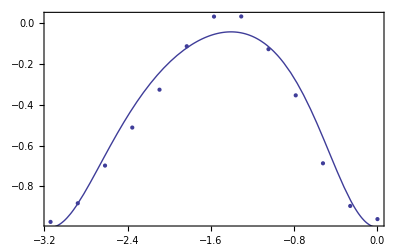

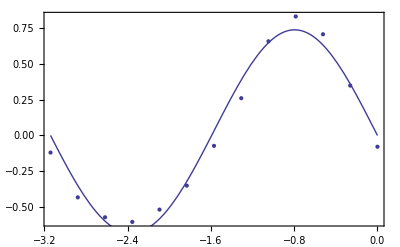

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
ma | -0.904167 | 2.40314×10^6 | {-5.35453×10^6,5.35452×10^6}
mb | 0.323854 | 860755. | {-1.91788×10^6,1.91788×10^6}
mc | -0.440185 | 1.16995×10^6 | {-2.6068×10^6,2.6068×10^6}

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
ma | -0.998861 | 2.51491×10^6 | {-5.60357×10^6,5.60357×10^6}
mb | -0.300335 | 756176. | {-1.68486×10^6,1.68486×10^6}
mc | 0.06379 | 160609. | {-357859.,357859.}

```mathematica
k=11.5;
p1datamagcalc={{0,-0.9599},{-0.2618,-0.89558},{-0.5236,-0.68676},{-0.7854,-0.35415},{-1.0472,-0.12816},{-1.309,0.03203},{-1.5708,0.03137},{-1.8326,-0.11378},{-2.0944,-0.3264},{-2.35619,-0.51177},{-2.61799,-0.69791},{-2.87979,-0.88236},{-3.14159,-0.97357}};
p2datamagcalc={{0,-0.0785},{-0.2618,0.3475},{-0.5236,0.7048},{-0.7854,0.82884},{-1.0472,0.65572},{-1.309,0.25953},{-1.5708,-0.07237},{-1.8326,-0.34954},{-2.0944,-0.51645},{-2.35619,-0.6021},{-2.61799,-0.57008},{-2.87979,-0.43126},{-3.14159,-0.11913}};
modelP1=P1datacalc[η,ma,mb,mc];
modelP2=P2datacalc[η,ma,mb,mc];

nlm1=NonlinearModelFit[p1datamagcalc,{modelP1,{-1.01<ma<1.01,-1.01<mb<1.01,-1.01<mc<1.01}},{ma,mb,mc},η,Method->"NMinimize"] 
nlm2=NonlinearModelFit[p2datamagcalc,{modelP2,{-1.01<ma<1.01,-1.01<mb<1.01,-1.01<mc<1.01}},{ma,mb,mc},η,Method->"NMinimize"] 
Show[ListPlot[p1datamagcalc],Plot[nlm1[η],{ η,-Pi,0}],Frame->True]
Show[ListPlot[p2datamagcalc],Plot[nlm2[η],{ η,-Pi,0}],Frame->True]
nlm1["FitResiduals"];
nlm2["FitResiduals"];
ListPlot[%,Filling->Axis];
nlm1["ParameterConfidenceIntervalTable"]
nlm2["ParameterConfidenceIntervalTable"]
```

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {7.40193×10^-6, 2.06209×10^-6, 2.34735×10^-6}, is returned.

FittedModel[-((Abs[(«19»+«1») «1»+«1»]^2-0.703894 («1»)^2) «1»)/(Abs[(«19»+«1») «1»+«1»]^2+0.703894 («1»)^2)+((«1»)«1»«1»)/(«1»+«1»)]

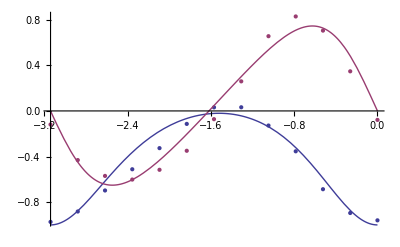

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
ma | 1.00491 | 1.53605×10^6 | {-3.17756×10^6,3.17757×10^6}
mb | -0.592861 | 906219. | {-1.87466×10^6,1.87466×10^6}
mc | 0.459207 | 701922. | {-1.45204×10^6,1.45204×10^6}

```mathematica
(*Sample data*)
SeedRandom[1];
dataf={{0,-0.9599},{-0.2618,-0.89558},{-0.5236,-0.68676},{-0.7854,-0.35415},{-1.0472,-0.12816},{-1.309,0.03203},{-1.5708,0.03137},{-1.8326,-0.11378},{-2.0944,-0.3264},{-2.35619,-0.51177},{-2.61799,-0.69791},{-2.87979,-0.88236},{-3.14159,-0.97357}};
datag={{0,-0.0785},{-0.2618,0.3475},{-0.5236,0.7048},{-0.7854,0.82884},{-1.0472,0.65572},{-1.309,0.25953},{-1.5708,-0.07237},{-1.8326,-0.34954},{-2.0944,-0.51645},{-2.35619,-0.6021},{-2.61799,-0.57008},{-2.87979,-0.43126},{-3.14159,-0.11913}};
modelP1=P1datacalc[η,ma,mb,mc];
modelP2=P2datacalc[η,ma,mb,mc];
(*Prepend 1 to data for f,2 to data for g*)
allData=Join[{1,Sequence@@#}&/@dataf,{2,Sequence@@#}&/@datag];

myF[η_,ma_,mb_,mc_,d_]:=KroneckerDelta[d-1]*P1datacalc[η,ma,mb,mc]+KroneckerDelta[d-2]*P2datacalc[η,ma,mb,mc]

nlm=NonlinearModelFit[allData,{myF[η,ma,mb,mc,d],{1.0<ma<1.01,-1.01<mb<1.01,-1.01<mc<1.01}},{ma,mb,mc},{d,η}]
Show[ListPlot[{dataf,datag}],Plot[{nlm[1,η],nlm[2,η]},{η,-Pi,0}]]
nlm["ParameterConfidenceIntervalTable"]
```

```mathematica
Manipulate[Dynamic@Show[Plot[{R*(P1datacalc[η,ma,mb,mc]),R*(P2datacalc[η,ma,mb,mc])},{ η,-Pi,0},Frame->True,AxesLabel->{"Eta angle (rad.)"},PlotLabel->Style["P2",FontSize->22],Background->LightGray,PlotStyle->{Blue,Dashed,Thick}],   p1datamag,p2datamag,PlotRange->{Automatic,{-1.1,1.1}},AxesOrigin->{0,0}],{ma,1.01,-1.01},{mb,1.01,-1.01},{mc,1.01,-1.01},{R,1,100}]
```

```mathematica
H=5 T;

ClearAll[P1,P2,P3,Z1,Z2,Z3,θ,F1,F2,A,h,k,l,θ,F1,F2,Za,Zb,Zc,P1,P2,P3,bet,alp,chi,za1,zb1,za2,zb2,zc1,zc2,ang1,ang2,ang3,ang4,z1,z2,z3,za1,za2,zb1,zb2,AA,g11,g21,g31,g12,g22,g23,g31,g32,g33,k,P1datacalc,P2datacalc,modelP1,modelP2,η,datafeh2,datageh2,ma,mb,mc,R,CS1pipi,CS2pipi,CS1pisi,CS2pisi,intensitydataeh2,g11,g12,g13,g21,g22,g23,g31,g32,g33,modeleh2,Intpipieh2,Intpisieh2,P1datacalceh2,P2datacalceh2]


θ[k_]:=9.7807+39.093 ⅇ^((k-15.5)/9.4701);
θ[15.5]=97.74863/2;
θ[16.5]=106.4565/2;
θ[17.5]=116.13412/2;

p1datamagh=ListPlot[{{0,1.0048},{-0.34907,0.838},{-0.69813,0.3548},{-1.0472,-0.3418},{-1.39626,-0.8423},{-1.74533,-0.7362},{-2.0944,-0.191},{-2.44346,0.4434},{-2.79253,0.8341},{-3.14159,1.0131}},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}];

p2datamagh=ListPlot[{{0,0.0654},{-0.34907,0.0715},{-0.69813,0.1125},{-1.0472,0.0594},{-1.39626,0.0938},{-1.74533,0.0777},{-2.0944,0.0855},{-2.44346,0.2032},{-2.79253,0.1096},{-3.14159,0.0557}},PlotStyle->Red,PlotMarkers->{Automatic,Medium}];

(* p1datamagh=ListPlot[{{0,-1.0048},{-0.34907,-0.838},{-0.69813,-0.3548},{-1.0472,0.3418},{-1.39626,0.8423},{-1.74533,0.7362},{-2.0944,0.191},{-2.44346,-0.4434},{-2.79253,-0.8341},{-3.14159,-1.0131}},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}];

p2datamagh=ListPlot[{{0,-0.0654},{-0.34907,-0.0715},{-0.69813,-0.1125},{-1.0472,-0.0594},{-1.39626,-0.0938},{-1.74533,-0.0777},{-2.0944,-0.0855},{-2.44346,-0.2032},{-2.79253,-0.1096},{-3.14159,-0.0557}},PlotStyle->Red,PlotMarkers->{Automatic,Medium}]; *)


r1={0,0.3748,1/4}; x=0;y=0.3748;z=1/4;
r2={0,-0.3748,3/4};
h=-0.5;
l=0.426;
A=1;
(*Fact1=(-za1 Cos[bet[k]]+zb1 Sin[bet[k]])*ⅇ^(2π ⅈ(h x+k y+l z));
Fact2=(-za2 Cos[bet[k]]+zb2 Sin[bet[k]])*ⅇ^(2π ⅈ(-h x-k y+l z+l/2-0.215));
Int=Lorentz[k]*Absorp[k]*ComplexExpand[Abs[(Fact1+Fact2)]]^2;*)

(*PolAnalyzer[η_]=1*{P1inci[η/2],P2inci[η/2]}; MatrixForm[PolAnalyzer[η]];*)
PolAnalyzer[η_]=1*{Cos[η],Sin[η]}; MatrixForm[PolAnalyzer[η]];

P1inci[η_]:=(A01+A11*Sin[Pi*(η-xc1)/(w1)]);
A01=0.03241; A11=0.98072;w1=89.34987*Pi/180;xc1=-46.31064*Pi/180;

P2inci[η_]:=(A02+A12*Sin[Pi*(η-xc2)/(w2)]);
A02=0.02268; A12=0.95145;w2=90.42687*Pi/180;xc2=-0.42663*Pi/180;


CS1pipi[k_,ma_,mb_,mc_]:={0,z21[k,ma,mb,mc] Sin[2θ[k]*π/180],0}ⅇ^(2π ⅈ(h x + k y + l z))
CS2pipi[k_,ma_,mb_,mc_]:={0,z22[k,ma,mb,mc] Sin[2θ[k]*π/180],0}ⅇ^(2π ⅈ(-h x - k y + l( z + 1/2)))*ⅇ^(-2π ⅈ 0.215)
CS1pisi[k_,ma_,mb_,mc_]:={z11[k,ma,mb,mc] Cos[θ[k]*π/180],0,z31[k,ma,mb,mc]Sin[θ[k]*π/180]}ⅇ^(2π ⅈ(h x + k y + l z))
CS2pisi[k_,ma_,mb_,mc_]:={z12[k,ma,mb,mc] Cos[θ[k]*π/180],0,z32[k,ma,mb,mc]Sin[θ[k]*π/180]}ⅇ^(2π ⅈ(-h x - k y + l( z + 1/2)))*ⅇ^(-2π ⅈ 0.215)

Intpipieh2[k_,ma_,mb_,mc_,R_]:=R Abs[(CS1pipi[k,ma,mb,mc] +CS2pipi[k,ma,mb,mc] ).(Conjugate[ CS1pipi[k,ma,mb,mc] + CS2pipi[k,ma,mb,mc] ])] 
Intpisieh2[k_,ma_,mb_,mc_,R_]:=R Abs[(CS1pisi[k,ma,mb,mc] +CS2pisi[k,ma,mb,mc] ).(Conjugate[ CS1pisi[k,ma,mb,mc] + CS2pisi[k,ma,mb,mc] ])] 

B1[k_,ma_,mb_,mc_]:=0;
B2[k_,ma_,mb_,mc_]:=(z11[k,ma,mb,mc]Cos[θ[k]*π/180]+z31[k,ma,mb,mc] Sin[θ[k]*Pi/180])*ⅇ^(2π ⅈ(h x+k y+l z))-(z12[k,ma,mb,mc] Cos[θ[k]*π/180]+z32[k,ma,mb,mc] Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(-h x-k y+l (z+1/2)-0.215A));
B3[k_,ma_,mb_,mc_]:=(-z11[k,ma,mb,mc]Cos[θ[k]*π/180]+z31[k,ma,mb,mc]Sin[θ[k]*Pi/180])*ⅇ^(2π ⅈ(h x+k y+l z))-(-z12[k,ma,mb,mc] Cos[θ[k]*π/180]+z32[k,ma,mb,mc] Sin[θ[k]*π/180])*ⅇ^(2π ⅈ(-h x-k y+l( z+1/2)-0.215 A)); (*SigmaPi component only*)
B4[k_,ma_,mb_,mc_]:=-z21[k,ma,mb,mc] Sin[2 θ[k]*π/180]*ⅇ^(2π ⅈ(h x+k y+l z))-z22[k,ma,mb,mc] Sin[2 θ[k]*π/180]*ⅇ^(2π ⅈ(-h x-k y+l (z+1/2)-0.215 A));
B[k_,ma_,mb_,mc_]=  {{B1[k,ma,mb,mc],B2[k,ma,mb,mc]},{B3[k,ma,mb,mc],B4[k,ma,mb,mc]}};


g11[k_]:=-0.07222-4.71694*10^-12 ⅇ^(k/0.84755);   g12[k_]:=-0.02089-1.42567 ⅇ^(-k/2.73703);  g13[k_]:=0.85503-310746.0871 ⅇ^(-k/0.74417);  
g21[k_]:=-1.37515+1.02491 ⅇ^(-k/2.72679);  g22[k_]:=-0.02194-0.15347 ⅇ^(-k/7.73823);   g23[k_]:=-0.0517;
g31[k_]:=0.09562+0.71958 ⅇ^(-k/6.58943);  g32[k_]:=-0.36969+0.07948 ⅇ^(-k/4.07494);   g33[k_]:=-0.04254-1.75835 ⅇ^(-k/3.08137);



(*g11[15.5]=-0.07263454;   g12[15.5]=-0.02583927;  g13[15.5]=0.85474958;  
g21[15.5]=-1.37166387;  g22[15.5]=-0.04264515;   g23[15.5]=-0.05172612;
g31[15.5]=0.16408998;  g32[15.5]=-0.36791789;   g33[15.5]=-0.05403443;

g11[16.5]=-0.07356559;   g12[16.5]=-0.0243244;  g13[16.5]=0.85495632;  
g21[16.5]=-1.3727333;  g22[16.5]=-0.04013498;   g23[16.5]=-0.05153872;
g31[16.5]=0.15444892;  g32[16.5]=-0.36830335;   g33[16.5]=-0.05084882;

g11[17.5]=-0.07659518;   g12[17.5]=-0.02327316;  g13[17.5]=0.85501025;  
g21[17.5]=-1.37347441;  g22[17.5]=-0.03792911;   g23[17.5]=-0.05284803;
g31[17.5]=0.14616536;  g32[17.5]=-0.36860493;   g33[17.5]=-0.04854605;*)


Trans2[k_]:={{g11[k],g12[k],g13[k]},{g21[k],g22[k],g23[k]},{g31[k],g32[k],g33[k]}}  (* Transformation from the ... to ... *)
Trans2[k]//MatrixForm;


magmoment[ma_,mb_,mc_]:={ma,mb,mc};
projectedmagmoment[k_,ma_,mb_,mc_]:=Trans2[k].magmoment[ma,mb,mc];
projectedmagmomentalongu1[k_,ma_,mb_,mc_]:=projectedmagmoment[k,ma,mb,mc][[1]]
projectedmagmomentalongu2[k_,ma_,mb_,mc_]:=projectedmagmoment[k,ma,mb,mc][[2]]
projectedmagmomentalongu3[k_,ma_,mb_,mc_]:=projectedmagmoment[k,ma,mb,mc][[3]]
z11[k_,ma_,mb_,mc_]:=projectedmagmomentalongu1[k,ma,mb,mc]
z21[k_,ma_,mb_,mc_]:=projectedmagmomentalongu2[k,ma,mb,mc]
z31[k_,ma_,mb_,mc_]:=projectedmagmomentalongu3[k,ma,mb,mc]
z12[k_,ma_,mb_,mc_]=-z11[k,ma,mb,mc];
z22[k_,ma_,mb_,mc_]=-z21[k,ma,mb,mc];
z32[k_,ma_,mb_,mc_]=z31[k,ma,mb,mc];




(*ma=0;mb=0.5;mc=0.5; R=1;*)
(*Intpipieh2[15.5,ma,mb,mc,R]/Intpipieh2[15.5,ma,mb,mc,R]*100;
Intpipieh2[16.5,ma,mb,mc,R]/Intpipieh2[15.5,ma,mb,mc,R]*100;
Intpipieh2[17.5,ma,mb,mc,R]/Intpipieh2[15.5,ma,mb,mc,R]*100;*)


 MatrixForm[B[z11,z31,z12,z32,z21,z22,A]];
MagMatrix[[1]];
Simplify[Abs[MagMatrix[[1]]]^2];
MagMatrix[[2]];
MatrixForm[PolAnalyzer[η]];

Μm[k,ma,mb,mc]=B[k,ma,mb,mc].PolAnalyzer[η];  MatrixForm[Μm[k,ma,mb,mc]];
MagMatrix=Μm[k,ma,mb,mc];


M1=MagMatrix[[1]];
Abs[M2]^2;
M2=MagMatrix[[2]];

P1primemag=Simplify[(Abs[M1]^2-Abs[M2]^2)/(Abs[M1]^2+Abs[M2]^2)] ;(* P1 component *)
                                 
P2primemag=Simplify[(Abs[M1+M2]^2-Abs[M1-M2]^2)/(Abs[M1+M2]^2+Abs[M1-M2]^2)] ;         (* P2 component *)     

P1datacalceh2[η_,ma_,mb_,mc_]=Simplify[(Abs[M1]^2-Abs[M2]^2)/(Abs[M1]^2+Abs[M2]^2)] ;
P2datacalceh2[η_,ma_,mb_,mc_]=Simplify[(Abs[M1+M2]^2-Abs[M1-M2]^2)/(Abs[M1+M2]^2+Abs[M1-M2]^2)]  ;
```

```mathematica
R=1;ma=1; mb=-0.6;mc=1;
Intpipieh2[15.5,ma,mb,mc,R]/Intpisieh2[15.5,ma,mb,mc,R]
Intpipieh2[16.5,ma,mb,mc,R]/Intpisieh2[16.5,ma,mb,mc,R]
Intpipieh2[17.5,ma,mb,mc,R]/Intpisieh2[17.5,ma,mb,mc,R]
```

6.72867

7.52683

2.46697

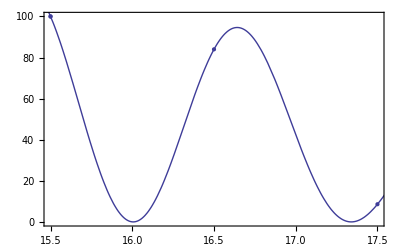

{-0.000584171,0.000259978,-0.0004007,-0.000584171}

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
ma | 0.0375853 | 28.2389 | {-358.771,358.846}
mb | 0.0172164 | 12.9031 | {-163.932,163.966}
mc | -1.01 | 758.647 | {-9640.53,9638.51}

```mathematica
modeleh2=100*Intpipieh2[k,ma,mb,mc,R]/Intpipieh2[15.5,ma,mb,mc,R]; R=1; 
intensitydataeh2={{15.5,100},{16.5,84},{17.5,8.6},{15.5,100}};
nlm=NonlinearModelFit[intensitydataeh2,{modeleh2,{-1.01<ma<1.01,-1.01<mb<1.01,-1.01<mc<1.01}},{ma,mb,mc},k,Method->"NMinimize"] ;
Show[ListPlot[intensitydataeh2],Plot[nlm[k],{k,14.5,18.5}],Frame->True]

nlm["FitResiduals"]
ListPlot[%,Filling->Axis];
nlm["ParameterConfidenceIntervalTable"]
```

FittedModel[(-Abs[(-«19»+«1») «1»+«1»]^2+0.113469 («1»)^2)/(Abs[«1»]^2+0.113469 Abs[«1»]^2)]

FittedModel[(-Abs[(«20»-«1») «1»+«1»]^2+Abs[«1»+«1»]^2)/(Abs[«1»]^2+Abs[«1»]^2)]

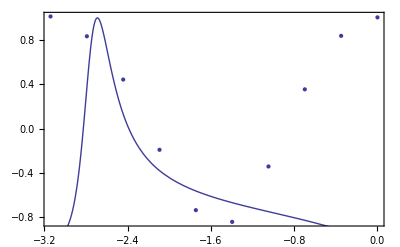

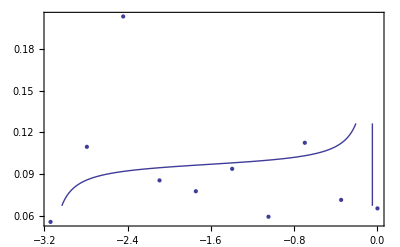

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
ma | 0.250629 | 4.08574×10^6 | {-9.66124×10^6,9.66124×10^6}
mb | 0.759564 | 1.61323×10^7 | {-3.81467×10^7,3.81467×10^7}
mc | 0.0442596 | 6.2973×10^7 | {-1.48908×10^8,1.48908×10^8}

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
ma | 1.00074 | 1.80456×10^6 | {-4.2671×10^6,4.2671×10^6}
mb | 0.191562 | 713434. | {-1.687×10^6,1.687×10^6}
mc | 0.0908298 | 2.6802×10^6 | {-6.33765×10^6,6.33766×10^6}

```mathematica
k=15.5;
datafeh2={{0,1.0048},{-0.34907,0.838},{-0.69813,0.3548},{-1.0472,-0.3418},{-1.39626,-0.8423},{-1.74533,-0.7362},{-2.0944,-0.191},{-2.44346,0.4434},{-2.79253,0.8341},{-3.14159,1.0131}};
datageh2={{0,0.0654},{-0.34907,0.0715},{-0.69813,0.1125},{-1.0472,0.0594},{-1.39626,0.0938},{-1.74533,0.0777},{-2.0944,0.0855},{-2.44346,0.2032},{-2.79253,0.1096},{-3.14159,0.0557}};
modelP1=P1datacalceh2[η,ma,mb,mc];
modelP2=P2datacalceh2[η,ma,mb,mc];

nlm1=NonlinearModelFit[datafeh2,{modelP1,{-1.01<ma<1.01,-1.01<mb<1.01,-1.01<mc<1.01}},{ma,mb,mc},η,Method->"NMinimize"] 
nlm2=NonlinearModelFit[datageh2,{modelP2,{-1.01<ma<1.01,-1.01<mb<1.01,-1.01<mc<1.01}},{ma,mb,mc},η,Method->"NMinimize"] 
Show[ListPlot[datafeh2],Plot[nlm1[η],{ η,-Pi,0}],Frame->True]
Show[ListPlot[datageh2],Plot[nlm2[η],{ η,-Pi,0}],Frame->True]
nlm1["FitResiduals"];
nlm2["FitResiduals"];
ListPlot[%,Filling->Axis];
nlm1["ParameterConfidenceIntervalTable"]
nlm2["ParameterConfidenceIntervalTable"]
```

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {2.30779×10^-6, 0.000478762, 7.89197×10^-7}, is returned.

FittedModel[((-Abs[(-«20»-«1») «1»+«1»]^2+0.013844 «1») «1»)/(Abs[(-«20»-«1») «1»+«1»]^2+0.013844 («1»)^2)+(«1»)/(«1»+«1»)]

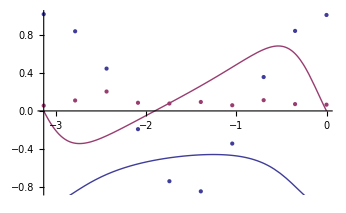

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
ma | 0.0688718 | 855706. | {-1.80538×10^6,1.80538×10^6}
mb | -0.0548936 | 682032. | {-1.43896×10^6,1.43896×10^6}
mc | 0.28131 | 3.49517×10^6 | {-7.37417×10^6,7.37417×10^6}

```mathematica
SeedRandom[1];
datafeh2={{0,1.0048},{-0.34907,0.838},{-0.69813,0.3548},{-1.0472,-0.3418},{-1.39626,-0.8423},{-1.74533,-0.7362},{-2.0944,-0.191},{-2.44346,0.4434},{-2.79253,0.8341},{-3.14159,1.0131}};
datageh2={{0,0.0654},{-0.34907,0.0715},{-0.69813,0.1125},{-1.0472,0.0594},{-1.39626,0.0938},{-1.74533,0.0777},{-2.0944,0.0855},{-2.44346,0.2032},{-2.79253,0.1096},{-3.14159,0.0557}};
modelP1=P1datacalceh2[η,ma,mb,mc];
modelP2=P2datacalceh2[η,ma,mb,mc];
(*Prepend 1 to data for f,2 to data for g*)
allData=Join[{1,Sequence@@#}&/@datafeh2,{2,Sequence@@#}&/@datageh2];

myF[η_,ma_,mb_,mc_,d_]:=KroneckerDelta[d-1]*P1datacalceh2[η,ma,mb,mc]+KroneckerDelta[d-2]*P2datacalceh2[η,ma,mb,mc]

nlm=NonlinearModelFit[allData,{myF[η,ma,mb,mc,d],{-1.0<ma<1.01,-1.01<mb<1.01,-1.01<mc<1.01}},{ma,mb,mc},{d,η}]
Show[ListPlot[{datafeh2,datageh2}],Plot[{nlm[1,η],nlm[2,η]},{η,-Pi,0}]]
nlm["ParameterConfidenceIntervalTable"]
```

```mathematica
Manipulate[Dynamic@Show[Plot[{R*(P1datacalceh2[η,ma,mb,mc]),R*(P2datacalceh2[η,ma,mb,mc])},{ η,-Pi,0},Frame->True,AxesLabel->{"Eta angle (rad.)"},PlotLabel->Style["P2",FontSize->22],Background->LightGray,PlotStyle->{Blue,Dashed,Thick}],   p1datamagh,p2datamagh,PlotRange->{Automatic,{-1.1,1.1}},AxesOrigin->{0,0}],{ma,1.01,-1.01},{mb,1.01,-1.01},{mc,1.01,-1.01},{R,1,100}]
```

```mathematica
Manipulate[Dynamic@Show[Plot[{R*((Abs[((0.117069+0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (-0.134678 za2+0.990889 zb2)) (-0.004-0.946 Sin[0.0242943-1.00112 η])]^2-Abs[((-0.232005-0.131947 I) zc1+(0.266105-0.0206065 I) E^((0.-1.35088 I) A) zc2) (-0.004-0.946 Sin[0.0242943-1.00112 η])+((-0.117069-0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (0.134678 za2+0.990889 zb2)) (0.0467+0.9493 Sin[1.53099+1.00113 η])]^2)/(Abs[((0.117069+0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (-0.134678 za2+0.990889 zb2)) (-0.004-0.946 Sin[0.0242943-1.00112 η])]^2+Abs[((-0.232005-0.131947 I) zc1+(0.266105-0.0206065 I) E^((0.-1.35088 I) A) zc2) (-0.004-0.946 Sin[0.0242943-1.00112 η])+((-0.117069-0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (0.134678 za2+0.990889 zb2)) (0.0467+0.9493 Sin[1.53099+1.00113 η])]^2)),R*((-Abs[((0.117069+0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (-0.134678 za2+0.990889 zb2)) (-0.004-0.946 Sin[0.0242943-1.00112 η])-((-0.232005-0.131947 I) zc1+(0.266105-0.0206065 I) E^((0.-1.35088 I) A) zc2) (-0.004-0.946 Sin[0.0242943-1.00112 η])-((-0.117069-0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (0.134678 za2+0.990889 zb2)) (0.0467+0.9493 Sin[1.53099+1.00113 η])]^2+Abs[((0.117069+0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (-0.134678 za2+0.990889 zb2)) (-0.004-0.946 Sin[0.0242943-1.00112 η])+((-0.232005-0.131947 I) zc1+(0.266105-0.0206065 I) E^((0.-1.35088 I) A) zc2) (-0.004-0.946 Sin[0.0242943-1.00112 η])+((-0.117069-0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (0.134678 za2+0.990889 zb2)) (0.0467+0.9493 Sin[1.53099+1.00113 η])]^2)/(Abs[((0.117069+0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (-0.134678 za2+0.990889 zb2)) (-0.004-0.946 Sin[0.0242943-1.00112 η])-((-0.232005-0.131947 I) zc1+(0.266105-0.0206065 I) E^((0.-1.35088 I) A) zc2) (-0.004-0.946 Sin[0.0242943-1.00112 η])-((-0.117069-0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (0.134678 za2+0.990889 zb2)) (0.0467+0.9493 Sin[1.53099+1.00113 η])]^2+Abs[((0.117069+0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (-0.134678 za2+0.990889 zb2)) (-0.004-0.946 Sin[0.0242943-1.00112 η])+((-0.232005-0.131947 I) zc1+(0.266105-0.0206065 I) E^((0.-1.35088 I) A) zc2) (-0.004-0.946 Sin[0.0242943-1.00112 η])+((-0.117069-0.0665803 I) za1-(0.861334+0.489863 I) zb1+(0.997015-0.0772063 I) E^((0.-1.35088 I) A) (0.134678 za2+0.990889 zb2)) (0.0467+0.9493 Sin[1.53099+1.00113 η])]^2))},{ η,-Pi,0},Frame->True,AxesLabel->{"Eta angle (rad.)"},PlotLabel->Style["P2",FontSize->22],Background->LightGray,PlotStyle->{Blue,Dashed,Thick}],   p1datamagh,p2datamagh,PlotRange->{Automatic,{-1.1,1.1}},AxesOrigin->{0,0}],{A,1,-1},{za1,1,-1},{za2,1,-1},{zb1,1,-1},{zb2,1,-1},{zc1,1,-1},{zc2,1,-1},{R,1,20}]
```

EuPtIn_mag_P2b.dat

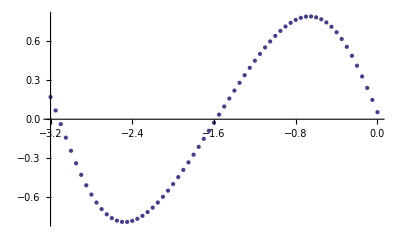

```mathematica
SetDirectory["D:\\Eu_SARAh\\Eu_moments"]; 
za1=0.5;za2=-0.5; zb1=0;zb2=0;zc1=1;zc2=1;
Intt=(Abs[0.+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (-0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (-0.968455343302662 za2+0.24918717468706747 zb2)) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])]^2-Abs[0.9 ((0.8063318480538441-0.4656485015026756 ⅈ) zc1-(0.2549973539017147-0.8955310858036913 ⅈ) zc2) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (0.968455343302662 za2+0.24918717468706747 zb2)) (0.0467+0.9493 Sin[2.0022692384702663 (0.7646287452987158+η/2)])]^2)/(Abs[0.+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (-0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (-0.968455343302662 za2+0.24918717468706747 zb2)) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])]^2+Abs[0.9 ((0.8063318480538441-0.4656485015026756 ⅈ) zc1-(0.2549973539017147-0.8955310858036913 ⅈ) zc2) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (0.968455343302662 za2+0.24918717468706747 zb2)) (0.0467+0.9493 Sin[2.0022692384702663 (0.7646287452987158+η/2)])]^2);

InttP2=((-Abs[0.+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (-0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (-0.968455343302662 za2+0.24918717468706747 zb2)) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])-0.9 ((0.8063318480538441-0.4656485015026756 ⅈ) zc1-(0.2549973539017147-0.8955310858036913 ⅈ) zc2) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])-0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (0.968455343302662 za2+0.24918717468706747 zb2)) (0.0467+0.9493 Sin[2.0022692384702663 (0.7646287452987158+η/2)])]^2+Abs[0.+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (-0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (-0.968455343302662 za2+0.24918717468706747 zb2)) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])+0.9 ((0.8063318480538441-0.4656485015026756 ⅈ) zc1-(0.2549973539017147-0.8955310858036913 ⅈ) zc2) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (0.968455343302662 za2+0.24918717468706747 zb2)) (0.0467+0.9493 Sin[2.0022692384702663 (0.7646287452987158+η/2)])]^2)/(Abs[0.+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (-0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (-0.968455343302662 za2+0.24918717468706747 zb2)) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])-0.9 ((0.8063318480538441-0.4656485015026756 ⅈ) zc1-(0.2549973539017147-0.8955310858036913 ⅈ) zc2) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])-0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (0.968455343302662 za2+0.24918717468706747 zb2)) (0.0467+0.9493 Sin[2.0022692384702663 (0.7646287452987158+η/2)])]^2+Abs[0.+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (-0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (-0.968455343302662 za2+0.24918717468706747 zb2)) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])+0.9 ((0.8063318480538441-0.4656485015026756 ⅈ) zc1-(0.2549973539017147-0.8955310858036913 ⅈ) zc2) (-0.004+0.946 Sin[2.002244738823859 (-0.01213352895986458+η/2)])+0.9 ((-0.8659730391584577+0.5000906872264913 ⅈ) (0.968455343302662 za1+0.24918717468706747 zb1)+(0.2738585038760456-0.9617699932181155 ⅈ) (0.968455343302662 za2+0.24918717468706747 zb2)) (0.0467+0.9493 Sin[2.0022692384702663 (0.7646287452987158+η/2)])]^2));
a=Table[InttP2,{η,0,-3.2,-0.05}];
b=Range[0,-3.2,-0.05];
c=Transpose[{b,a}];
Export["EuPtIn_mag_P2b.dat",c]
ListPlot[c]
```

```mathematica
a1=4.542; b1=16.85; c1=7.389;
Angl[h1_,k1_,l1_,h2_,k2_,l2_]:=ArcCos[ ({h1/a1,k1/b1,l1/c1}.{h2/a1,k2/b1,l2/c1})/(√((h1/a1)^2+(k1/b1)^2+(l1/c1)^2)*√((h2/a1)^2+(k2/b1)^2+(l2/c1)^2))]*180/π

Angl[1,-0.598,0,-0.5,-11.5,-0.4258]
```

90.0057

```mathematica
Angl[1.9,0.1,0,-0.0434,-0.998,-0.0373]
```

99.9418

```mathematica
Angl[0,-0.1895,1,0.043478,1,0.037391]
```

89.8782

```mathematica
ClearAll[k2,l2,h2]
h1=-0.5;k1=-11.5;l1=-0.4258; h3=1;k3=-0.6;l3=0; l2=1;
NSolve[{ArcCos[ ({h1/a1,k1/b1,l1/c1}.{h2/a1,k2/b1,l2/c1})/(√((h1/a1)^2+(k1/b1)^2+(l1/c1)^2)*√((h2/a1)^2+(k2/b1)^2+(l2/c1)^2))]*180/π==90,ArcCos[ ({h3/a1,k3/b1,l3/c1}.{h2/a1,k2/b1,l2/c1})/(√((h3/a1)^2+(k3/b1)^2+(l3/c1)^2)*√((h2/a1)^2+(k2/b1)^2+(l2/c1)^2))]*180/π==90},{h2,k2}]
```

{{h2→-0.00818084,k2→-0.187652}}

```mathematica
ClearAll[za,zb,zc,h,k,l]
h:=0;k:= 0;l:= 1;
NSolve[{h== za 0.85749-zb 0.0434069-zc 0.0080394,k== -za 0.51449-zb 0.9983-zc 0.18437,l== za 0-zb 0.037329+zc 0.9828},{za,zb,zc}]
```

{{za→0.0000262309,zb→-0.186621,zc→1.01041}}

```mathematica
ClearAll[za,zb,zc,h,k,l]
za:= 0.67(* z // a *);     zc:= 0.45(* z // c *);   zb:= -0.16 (* z // b *);
NSolve[{h== za 0.85749-zb 0.0434069-zc 0.0080394,k== -za 0.51449-zb 0.9983-zc 0.18437,l== za 0-zb 0.037329+zc 0.9828},{h,k,l}]
```

{{h→0.577846,k→-0.267947,l→0.448233}}

```mathematica
Normalize[{0.577846,-0.267947,0.448233}]  (* moment *)
```

{0.741918,-0.344027,0.575503}

```mathematica
h1=1;k1=-0.6;l1=0; h3=1/2;k3=23/2;l3=0.43; h2=1;
θ[k_]:=0.5*(-98.22284+105.69129*Exp[k/25.19289]);
alp[k_]:=24.79091+3.6745*Exp[k/7.28251];
bet[k_]:=(2*θ[k]-alp[k]);
θ[11.5]
alp[11.5]
bet[11.5]
```

34.3057

42.6149

25.9965

```mathematica
Normalize[{1,-0.6,0}]  (* U1 *)
Normalize[{-0.00818,-0.1876,1}]  (* U2 *)
Normalize[{-0.5,-11.5,-0.43}]    (* U3 *)
Normalize[{0,22.938,-121.04}]
Normalize[{-0.5,-11.5,-0.43}]
Normalize[{0.857,-0.325,-0.982}]
Normalize[{1,-0.6,-0.0}]
Normalize[{0.1779,-0.3,1}]
Normalize[{0.1406,-0.276,1}]
Normalize[{1.1406,-0.797,0.6}]
Normalize[{1,22.938,-121.043}]
Normalize[{1,-0.8,1.05}]
Normalize[{-0.394,0.04335,1}]
```

{0.857493,-0.514496,0.}

{-0.00803949,-0.184378,0.982823}

{-0.0434069,-0.99836,-0.03733}

{0.,0.186194,-0.982513}

{-0.0434069,-0.99836,-0.03733}

{0.637991,-0.241945,-0.731047}

{0.857493,-0.514496,0.}

{0.167976,-0.283265,0.944217}

{0.134305,-0.263642,0.955225}

{0.752715,-0.525963,0.395957}

{0.0081168,0.186183,-0.982482}

{0.603847,-0.483077,0.634039}

{-0.366276,0.0402996,0.929633}

```mathematica
θ[k_]:=(-98.22284+105.69129*Exp[k/25.19289]);
alp[k_]:=24.79091+3.6745*Exp[k/7.28251];
bet[k_]:=(2*θ[k]-alp[k]);
bet[6.5]
bet[7.5]
bet[8.5]
bet[9.5]
bet[10.5]
bet[11.5]
bet[12.5]
bet[13.5]
bet[14.5]
```

43.3959

53.1543

63.1669

73.4233

83.9096

94.6079

105.495

116.544

127.718